```mathematica
Solve[Element[x1|x2|x3,Integers]
&&(1≤x1≤4)
&&(1≤x2≤4)
&&(1≤x3≤4)
&&(x1≠x2)
&&(x2≠x3)
&&(x3≠x1),{x1,x2,x3}]
```

{{x1→1,x2→2,x3→3},{x1→1,x2→2,x3→4},{x1→1,x2→3,x3→2},{x1→1,x2→3,x3→4},{x1→1,x2→4,x3→2},{x1→1,x2→4,x3→3},{x1→2,x2→1,x3→3},{x1→2,x2→1,x3→4},{x1→2,x2→3,x3→1},{x1→2,x2→3,x3→4},{x1→2,x2→4,x3→1},{x1→2,x2→4,x3→3},{x1→3,x2→1,x3→2},{x1→3,x2→1,x3→4},{x1→3,x2→2,x3→1},{x1→3,x2→2,x3→4},{x1→3,x2→4,x3→1},{x1→3,x2→4,x3→2},{x1→4,x2→1,x3→2},{x1→4,x2→1,x3→3},{x1→4,x2→2,x3→1},{x1→4,x2→2,x3→3},{x1→4,x2→3,x3→1},{x1→4,x2→3,x3→2}}

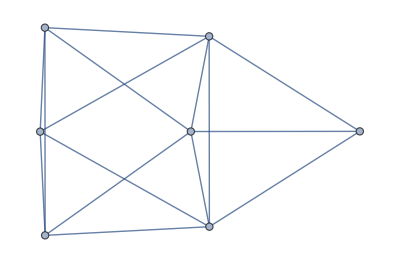

```mathematica
graf6=Graph[{1<->2,1<->3,1<->5,1<->7,2<->3,2<->6,2<->7,3<->4,3<->5,3<->6,4<->5,4<->6,5<->6,5<->7,6<->7}]
```

```mathematica
ToVars[g_]:=Block[{exp,sep,vertex, vertices,var,var1, var2,  edges, edgeIndex, edge},
(* works only for graphs in which 1,2 and 3 are connected *)
exp= "Solve[";
sep="";
vertices=VertexList[g];
For[vertex=1,vertex<=Length[vertices], vertex++,
var ="x" <> ToString[ vertices[[vertex]] ];
exp= exp<>sep<> "Element["<>var<>", Integers]";
sep=" && " 
];

For[vertex=1,vertex<=Length[vertices], vertex++,
var ="x" <> ToString[ vertices[[vertex]] ];
exp= exp<>sep<> "(1<="<>var<>" <=4)";
sep=" && " 
];

edges=EdgeList[g];

exp= exp<>sep<> "x1 == 1 && x2== 2 && x3==3";
sep=" && " ;

For[edgeIndex=1,edgeIndex≤Length[edges],edgeIndex++,
edge=edges[[edgeIndex]];
var1 ="x" <> ToString[ edge[[1]] ];
var2 ="x" <> ToString[ edge[[2]] ];
exp= exp<>sep<> var1<>"!="<>var2;
sep=" && " 
];
exp=exp <> ", {";
sep="";
For[vertex=1,vertex<=Length[vertices], vertex++,
var ="x" <> ToString[ vertices[[vertex]] ];
exp= exp<>sep<> var;
sep=", " 
];
exp=exp <> "}]";
Return[Read[ StringToStream[ exp],Expression]]
]
```

```mathematica
ToColors[l_]:=Block[{index, val, color, var, result, sep},
result="{";
sep="";
For[index=1,index≤Length[l],index++,
var = StringDrop [ToString[l[[index,1]]],1];
color= {"Red","Green","Blue", "Yellow"} [[  l[[index,2]] ]];
result=result<>sep<> var <>"->" <> color;
sep=", "
];
result=result <>"}";
Return[Read[ StringToStream[ result],Expression]]
]
```

```mathematica
PaintGraph[g_, opts__]:=Block[{sols},
sols=ToVars[g];
{Map[
VertexDelete[Graph[g,PlotLabel->ChromaticPolynomial[g,4],ImageSize->250, GraphLayout->"PlanarEmbedding", VertexStyle->ToColors[#], VertexLabels->"Name", VertexSize->Medium, opts],{1,2,3}]&
,sols],
Map[
Graph[g,PlotLabel->ChromaticPolynomial[g,4],ImageSize->250, GraphLayout->"PlanarEmbedding", VertexStyle->ToColors[#], VertexLabels->"Name", VertexSize->Medium, opts]&
,sols]}
]
```

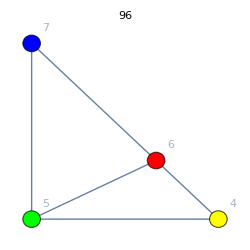
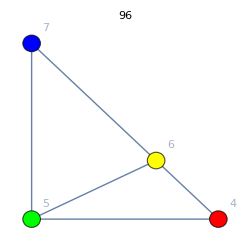
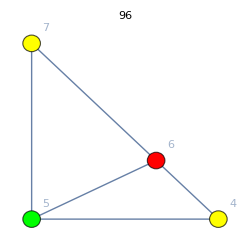
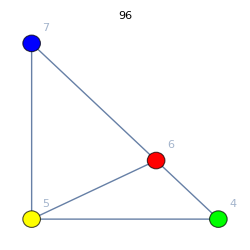
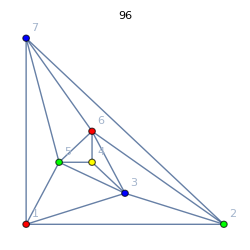
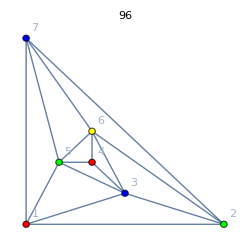
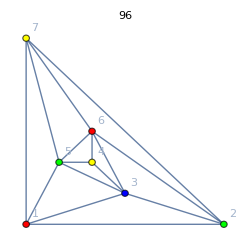
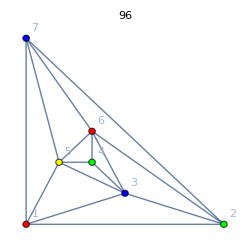

```mathematica
PaintGraph[graf6]
```

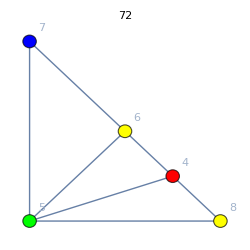
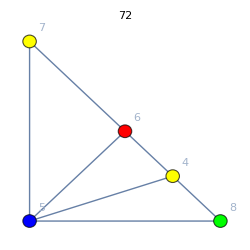
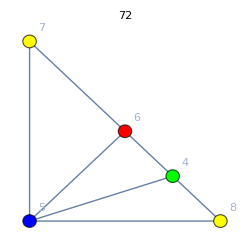
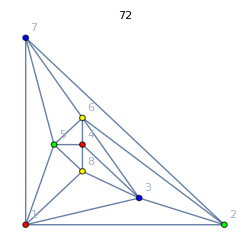
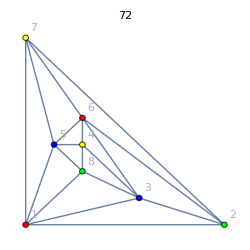
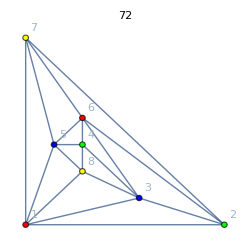

```mathematica
PaintGraph[graf18]
```

```mathematica
Map[ToColors[#]&,ToVars[graf18]]
```

{{1→RGBColor[1, 0, 0],2→RGBColor[0, 1, 0],3→RGBColor[0, 0, 1],5→RGBColor[0, 1, 0],7→RGBColor[0, 0, 1],8→RGBColor[1, 1, 0],6→RGBColor[1, 1, 0],4→RGBColor[1, 0, 0]},{1→RGBColor[1, 0, 0],2→RGBColor[0, 1, 0],3→RGBColor[0, 0, 1],5→RGBColor[0, 0, 1],7→RGBColor[1, 1, 0],8→RGBColor[0, 1, 0],6→RGBColor[1, 0, 0],4→RGBColor[1, 1, 0]},{1→RGBColor[1, 0, 0],2→RGBColor[0, 1, 0],3→RGBColor[0, 0, 1],5→RGBColor[0, 0, 1],7→RGBColor[1, 1, 0],8→RGBColor[1, 1, 0],6→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0]}}

{1->Red, 2->Green, 3->Blue, 5->Green, 7->Blue, 6->Red, 4->Yellow}

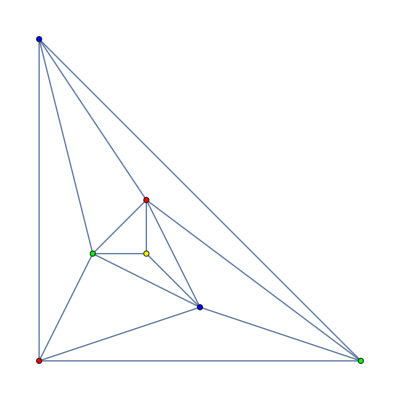

```mathematica
Graph[graf6,GraphLayout->"PlanarEmbedding", VertexStyle->ToColors[{x1->1,x2->2,x3->3,x5->2,x7->3,x6->1,x4->4}]]
```

```mathematica
ToColors[{x1->1,x2->2,x3->3,x5->2,x7->3,x6->1,x4->4}]
```

1

Red

2

Green

3

Blue

5

Green

7

Blue

6

Red

4

Black

{1->Red, 2->Green, 3->Blue, 5->Green, 7->Blue, 6->Red, 4->Black}

{1→RGBColor[1, 0, 0],2→RGBColor[0, 1, 0],3→RGBColor[0, 0, 1],5→RGBColor[0, 1, 0],7→RGBColor[0, 0, 1],6→RGBColor[1, 0, 0],4→GrayLevel[0]}

```mathematica
ToVars[graf6]
```

{{x1→1,x2→2,x3→3,x5→2,x7→3,x6→1,x4→4},{x1→1,x2→2,x3→3,x5→2,x7→3,x6→4,x4→1},{x1→1,x2→2,x3→3,x5→2,x7→4,x6→1,x4→4},{x1→1,x2→2,x3→3,x5→4,x7→3,x6→1,x4→2}}

```mathematica
ToVars[graf18]
```

{{x1→1,x2→2,x3→3,x5→2,x7→3,x8→4,x6→4,x4→1},{x1→1,x2→2,x3→3,x5→3,x7→4,x8→2,x6→1,x4→4},{x1→1,x2→2,x3→3,x5→3,x7→4,x8→4,x6→1,x4→2}}

```mathematica
ChromaticPolynomial[graf6,4]/24
```

4

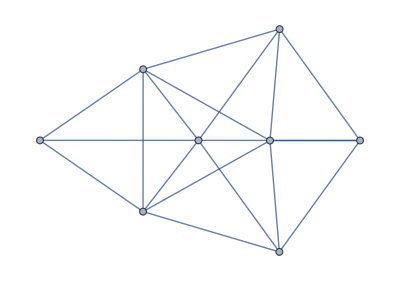

```mathematica
graph11=Graph[{1<->2,1<->3,1<->7,2<->3,2<->5,2<->6,2<->7,3<->4,3<->6,3<->7,3<->8,4<->5,4<->6,4<->8,5<->6,5<->7,5<->8,7<->8}]
```

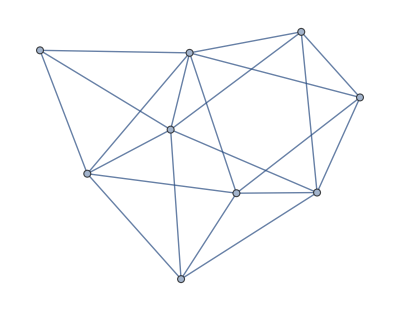

```mathematica
graph40=Graph[{1<->2,1<->3,1<->7,2<->3,2<->5,2<->6,2<->7,2<->9,3<->4,3<->7,3<->8,3<->9,4<->5,4<->6,4<->8,4<->9,5<->6,5<->7,5<->8,6<->9,7<->8}]
```

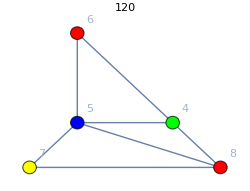
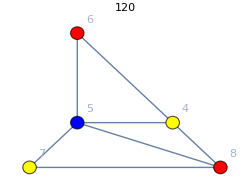
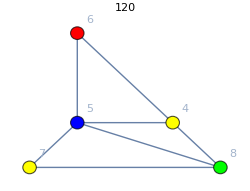
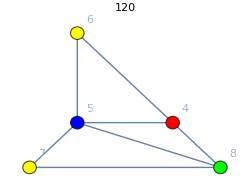
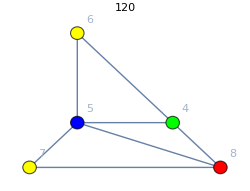
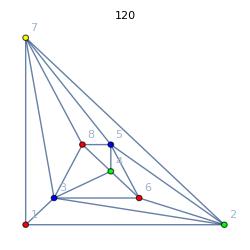
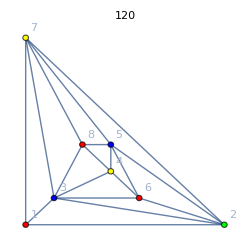
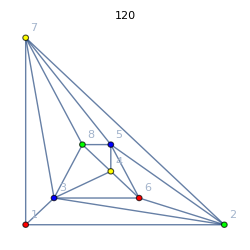

```mathematica
PaintGraph[graph11]
```

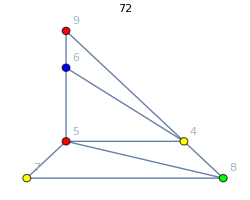
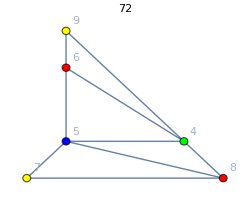
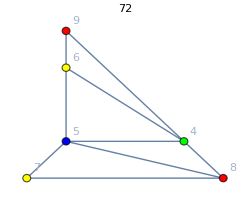
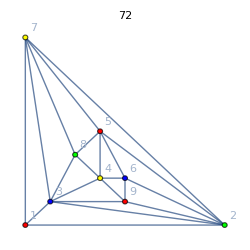
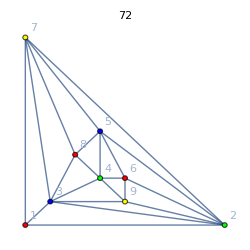
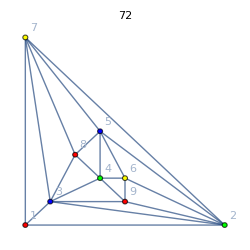

```mathematica
PaintGraph[graph40]
```